```mathematica
CompleteBaseCoeff[ x^5-5 x^4+10 x^3-10 x^2+4 x]
```

{0,0,0,5,5,1}

```mathematica
Select[Keys[allGraphs6],CompleteBaseCoeff[ ChromaticPolynomial[ allGraphs6[#,"graph"],x]]=={0,0,0,0,0,5,1}&]
```

$Aborted

```mathematica
Table[allGraphs6[k,"graph"],{k,}]
```

```mathematica
Monitor[TableForm[Table[CompleteBaseCoeff[ ChromaticPolynomial[ allGraphs6[k,"graph"],x]],{k,Sort[Keys[allGraphs6]]}]//Tally//Sort,TableDepth->2],k]
```

{0,1} | 1
{0,0,1} | 31
{0,1,1} | 31
{0,0,0,1} | 90
{0,0,1,1} | 270
{0,0,2,1} | 270
{0,1,3,1} | 90
{0,0,0,0,1} | 65
{0,0,0,1,1} | 390
{0,0,0,2,1} | 780
{0,0,0,3,1} | 260
{0,0,1,2,1} | 195
{0,0,1,3,1} | 1040
{0,0,2,4,1} | 975
{0,0,4,5,1} | 390
{0,1,7,6,1} | 65
{0,0,0,0,0,1} | 15
{0,0,0,0,1,1} | 150
{0,0,0,0,2,1} | 450
{0,0,0,0,3,1} | 300
{0,0,0,0,4,1} | 75
{0,0,0,1,2,1} | 225
{0,0,0,1,3,1} | 1050
{0,0,0,2,3,1} | 450
{0,0,0,2,4,1} | 2025
{0,0,0,3,4,1} | 900
{0,0,0,3,5,1} | 450
{0,0,0,4,5,1} | 2250
{0,0,0,5,5,1} | 180
{0,0,0,6,6,1} | 1050
{0,0,0,9,7,1} | 150
{0,0,1,4,4,1} | 150
{0,0,1,5,5,1} | 900
{0,0,1,7,6,1} | 1875
{0,0,2,7,6,1} | 225
{0,0,2,10,7,1} | 1650
{0,0,4,14,8,1} | 675
{0,0,8,19,9,1} | 150
{0,1,15,25,10,1} | 15
{0,0,0,0,0,0,1} | 1
{0,0,0,0,0,1,1} | 15
{0,0,0,0,0,2,1} | 60
{0,0,0,0,0,3,1} | 60
{0,0,0,0,0,4,1} | 30
{0,0,0,0,0,5,1} | 6
{0,0,0,0,1,2,1} | 45
{0,0,0,0,1,3,1} | 200
{0,0,0,0,2,3,1} | 180
{0,0,0,0,2,4,1} | 585
{0,0,0,0,3,4,1} | 420
{0,0,0,0,3,5,1} | 300
{0,0,0,0,4,4,1} | 90
{0,0,0,0,4,5,1} | 900
{0,0,0,0,4,6,1} | 60
{0,0,0,0,5,5,1} | 432
{0,0,0,0,6,6,1} | 960
{0,0,0,0,7,6,1} | 180
{0,0,0,0,8,7,1} | 180
{0,0,0,0,9,7,1} | 360
{0,0,0,0,12,8,1} | 135
{0,0,0,0,16,9,1} | 15
{0,0,0,1,3,3,1} | 15
{0,0,0,1,4,4,1} | 240
{0,0,0,1,5,5,1} | 720
{0,0,0,1,6,5,1} | 360
{0,0,0,1,7,6,1} | 1215
{0,0,0,1,8,6,1} | 360
{0,0,0,2,6,5,1} | 225
{0,0,0,2,7,5,1} | 60
{0,0,0,2,7,6,1} | 450
{0,0,0,2,8,6,1} | 1260
{0,0,0,2,9,6,1} | 60
{0,0,0,2,10,7,1} | 2460
{0,0,0,2,11,7,1} | 180
{0,0,0,3,9,6,1} | 360
{0,0,0,3,9,7,1} | 90
{0,0,0,3,11,7,1} | 1440
{0,0,0,3,13,8,1} | 420
{0,0,0,4,9,6,1} | 90
{0,0,0,4,11,7,1} | 900
{0,0,0,4,12,7,1} | 360
{0,0,0,4,14,8,1} | 2700
{0,0,0,5,12,7,1} | 360
{0,0,0,5,15,8,1} | 360
{0,0,0,6,14,8,1} | 180
{0,0,0,6,15,8,1} | 1980
{0,0,0,6,18,9,1} | 910
{0,0,0,7,16,8,1} | 180
{0,0,0,8,19,9,1} | 2160
{0,0,0,9,19,9,1} | 360
{0,0,0,9,23,10,1} | 90
{0,0,0,10,20,9,1} | 360
{0,0,0,12,24,10,1} | 1140
{0,0,0,15,25,10,1} | 72
{0,0,0,18,30,11,1} | 240
{0,0,0,27,37,12,1} | 20
{0,0,1,6,11,6,1} | 10
{0,0,1,7,13,7,1} | 90
{0,0,1,8,13,7,1} | 15
{0,0,1,8,16,8,1} | 180
{0,0,1,9,16,8,1} | 300
{0,0,1,10,20,9,1} | 60
{0,0,1,11,20,9,1} | 1080
{0,0,1,15,25,10,1} | 1296
{0,0,2,13,20,9,1} | 60
{0,0,2,16,25,10,1} | 405
{0,0,2,22,31,11,1} | 1080
{0,0,4,23,31,11,1} | 45
{0,0,4,32,38,12,1} | 435
{0,0,8,46,46,13,1} | 105
{0,0,16,65,55,14,1} | 15
{0,1,31,90,65,15,1} | 1

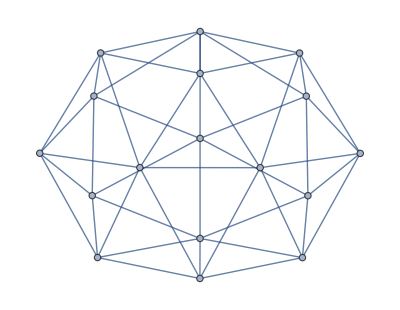

```mathematica
g=Graph[plantri[[8]]]
```

```mathematica
ToLogical[g_,max_:4]:=Block[{exp,vertex,vertices,var,var1,var2,edges,edgeIndex,edge},exp=True;
vertices=VertexList[g];
For[vertex=1,vertex≤Length[vertices],vertex++,var=Symbol["x"<>ToString[vertices[[vertex]]]];
exp=exp&&Element[var,Integers];];
For[vertex=1,vertex≤Length[vertices],vertex++,var=Symbol["x"<>ToString[vertices[[vertex]]]];
exp=exp&&(1≤var≤max);];
edges=EdgeList[g];
For[edgeIndex=1,edgeIndex≤Length[edges],edgeIndex++,edge=edges[[edgeIndex]];
var1=Symbol["x"<>ToString[edge[[1]]]];
var2=Symbol["x"<>ToString[edge[[2]]]];
exp=exp&&var1≠var2;];
exp]
```

```mathematica
exp=ToLogical[g,5]
```

x1∈Integers&&x2∈Integers&&x3∈Integers&&x4∈Integers&&x5∈Integers&&x6∈Integers&&x7∈Integers&&x8∈Integers&&x9∈Integers&&x10∈Integers&&x11∈Integers&&x12∈Integers&&x13∈Integers&&x14∈Integers&&x15∈Integers&&x16∈Integers&&x17∈Integers&&1≤x1≤5&&1≤x2≤5&&1≤x3≤5&&1≤x4≤5&&1≤x5≤5&&1≤x6≤5&&1≤x7≤5&&1≤x8≤5&&1≤x9≤5&&1≤x10≤5&&1≤x11≤5&&1≤x12≤5&&1≤x13≤5&&1≤x14≤5&&1≤x15≤5&&1≤x16≤5&&1≤x17≤5&&x1≠x2&&x1≠x3&&x1≠x4&&x1≠x5&&x1≠x6&&x2≠x6&&x2≠x7&&x2≠x8&&x2≠x3&&x3≠x8&&x3≠x9&&x3≠x10&&x3≠x4&&x4≠x10&&x4≠x11&&x4≠x12&&x4≠x5&&x5≠x12&&x5≠x13&&x5≠x6&&x6≠x13&&x6≠x7&&x7≠x13&&x7≠x14&&x7≠x15&&x7≠x8&&x8≠x15&&x8≠x9&&x9≠x15&&x9≠x16&&x9≠x10&&x10≠x16&&x10≠x11&&x11≠x16&&x11≠x17&&x11≠x12&&x12≠x17&&x12≠x14&&x12≠x13&&x13≠x14&&x14≠x17&&x14≠x15&&x15≠x17&&x15≠x16&&x16≠x17

```mathematica
36281*120
```

4353720

```mathematica
EdgeCount[g]
```

45

```mathematica
(CompleteBaseCoeff[ ChromaticPolynomial[g,x]]//Rest)
```

{0,0,0,22,36281,1796800,17198421,55339513,78241812,56479726,22766977,5401613,773706,66900,3380,91,1}

```mathematica
N[22*24/694337290,50]
```

7.604373373061959555708148701044127991454988684246×10^-7

```mathematica
Table[StirlingS2[17,k],{k,1,17}]
```

{1,65535,21457825,694337290,5652751651,17505749898,25708104786,20415995028,9528822303,2758334150,512060978,62022324,4910178,249900,7820,136,1}

```mathematica
NullBaseCoeff[ ChromaticPolynomial[g,x]]
```

{0,71265972,-351946840,802461675,-1131475014,1112163274,-812626569,458524982,-204408959,72889503,-20875904,4786421,-868885,122328,-12900,960,-45,1}

```mathematica
ChromaticPolynomial[g,4]
```

528

```mathematica
CompleteBaseCoeff[ ChromaticPolynomial[g2,x]]
```

{0,0,0,0,63,31366,906909,5851378,13552503,14251874,7761732,2362156,417968,43395,2575,80,1}

```mathematica
528/24
```

22

```mathematica
sols=ToVarsLogical[g,True]
```

{{x1→1,x2→2,x3→3,x4→2,x5→3,x6→4,x7→1,x8→4,x9→2,x10→1,x11→3,x12→1,x13→2,x14→4,x15→3,x16→4,x17→2},{x1→1,x2→2,x3→3,x4→2,x5→3,x6→4,x7→1,x8→4,x9→2,x10→4,x11→3,x12→1,x13→2,x14→4,x15→3,x16→1,x17→2},{x1→1,x2→2,x3→3,x4→2,x5→3,x6→4,x7→3,x8→1,x9→2,x10→4,x11→1,x12→4,x13→2,x14→1,x15→4,x16→3,x17→2},{x1→1,x2→2,x3→3,x4→2,x5→3,x6→4,x7→3,x8→1,x9→2,x10→4,x11→3,x12→4,x13→2,x14→1,x15→4,x16→1,x17→2},521,{x1→4,x2→3,x3→2,x4→3,x5→2,x6→1,x7→2,x8→4,x9→3,x10→1,x11→4,x12→1,x13→3,x14→4,x15→1,x16→2,x17→3},{x1→4,x2→3,x3→2,x4→3,x5→2,x6→1,x7→4,x8→1,x9→3,x10→1,x11→2,x12→4,x13→3,x14→1,x15→2,x16→4,x17→3},{x1→4,x2→3,x3→2,x4→3,x5→2,x6→1,x7→4,x8→1,x9→3,x10→4,x11→2,x12→4,x13→3,x14→1,x15→2,x16→1,x17→3}}
 |  |  |  |

```mathematica
Length[sols]
```

528

```mathematica
SolutionToPartition[ol_]:=Block[{assoc=Association[],i,val},
For[i=1,i≤4,i++,
assoc[i]={}
];
For[i=1,i≤Length[ol],i++,
val=ol[[i,2]];
assoc[val]=Append[assoc[val], IntegerString[i,10,2]]
];
Row[Riffle[Sort[Select[Table[StringRiffle[assoc[key],"-"],{key,Keys[assoc]}],#≠""&]],Style["♁",Bold,Red]]]
]
```

```mathematica
SolutionToPartition[ol_,vertices_]:=Block[{assoc=Association[],i,val},
For[i=1,i≤4,i++,
assoc[i]={}
];
Table[val=ol[[i,2]];
assoc[val]=Append[assoc[val], IntegerString[i,10,2]]
,{i,vertices}];
Row[Riffle[Sort[Select[Table[StringRiffle[assoc[key],"-"],{key,Keys[assoc]}],#≠""&]],Style["*",Red]]]
]
```

```mathematica
TextForm[2,"00"]
```

TextForm::argx: TextForm called with 2 arguments; 1 argument is expected.

TextForm[2, 00]

```mathematica
SolutionToPartition[{x1->1,x2->2,x3->3,x4->2,x5->3,x6->4,x7->1,x8->4,x9->2,x10->1,x11->3,x12->1,x13->2,x14->4,x15->3,x16->4,x17->2}]
```

```mathematica
TableForm[Map[SolutionToPartition[#]&,Take[sols,100]]]
```

01-07-10-12♁02-04-09-13-17♁03-05-11-15♁06-08-14-16
01-07-12-16♁02-04-09-13-17♁03-05-11-15♁06-08-10-14
01-08-11-14♁02-04-09-13-17♁03-05-07-16♁06-10-12-15
01-08-14-16♁02-04-09-13-17♁03-05-07-11♁06-10-12-15
01-10-12-15♁02-04-09-13-17♁03-05-07-11♁06-08-14-16
01-10-12-15♁02-04-09-13-17♁03-05-07-16♁06-08-11-14
01-07-10-12♁02-04-09-13-17♁03-06-11-15♁05-08-14-16
01-07-12-16♁02-04-09-13-17♁03-06-11-15♁05-08-10-14
01-08-10-13-17♁02-04-14-16♁03-06-12-15♁05-07-09-11
01-07-10-17♁02-05-09-11-14♁03-06-12-15♁04-08-13-16
01-08-10-13-17♁02-05-09-11-14♁03-06-12-15♁04-07-16
01-07-09-12♁02-05-10-17♁03-11-13-15♁04-06-08-14-16
01-07-10-12♁02-05-09-17♁03-11-13-15♁04-06-08-14-16
01-08-10-13-17♁02-05-09-11-14♁03-07-12-16♁04-06-15
01-08-10-13-17♁02-05-11-15♁03-07-12-16♁04-06-09-14
01-10-13-15♁02-05-09-11-14♁03-07-12-16♁04-06-08-17
01-07-09-12♁02-10-13-17♁03-05-11-15♁04-06-08-14-16
01-07-10-12♁02-09-13-17♁03-05-11-15♁04-06-08-14-16
01-09-11-13♁02-10-12-15♁03-05-07-17♁04-06-08-14-16
01-09-13-17♁02-10-12-15♁03-05-07-11♁04-06-08-14-16
01-10-12-15♁02-09-11-13♁03-05-07-17♁04-06-08-14-16
01-10-12-15♁02-09-13-17♁03-05-07-11♁04-06-08-14-16
01-07-10-12♁02-04-09-13-17♁03-06-11-15♁05-08-14-16
01-07-12-16♁02-04-09-13-17♁03-06-11-15♁05-08-10-14
01-08-10-13-17♁02-04-14-16♁03-06-12-15♁05-07-09-11
01-07-10-12♁02-04-09-13-17♁03-05-11-15♁06-08-14-16
01-07-12-16♁02-04-09-13-17♁03-05-11-15♁06-08-10-14
01-08-11-14♁02-04-09-13-17♁03-05-07-16♁06-10-12-15
01-08-14-16♁02-04-09-13-17♁03-05-07-11♁06-10-12-15
01-10-12-15♁02-04-09-13-17♁03-05-07-16♁06-08-11-14
01-10-12-15♁02-04-09-13-17♁03-05-07-11♁06-08-14-16
01-07-09-12♁02-05-10-17♁03-11-13-15♁04-06-08-14-16
01-07-10-12♁02-05-09-17♁03-11-13-15♁04-06-08-14-16
01-08-10-13-17♁02-05-09-11-14♁03-07-12-16♁04-06-15
01-08-10-13-17♁02-05-11-15♁03-07-12-16♁04-06-09-14
01-10-13-15♁02-05-09-11-14♁03-07-12-16♁04-06-08-17
01-07-10-17♁02-05-09-11-14♁03-06-12-15♁04-08-13-16
01-08-10-13-17♁02-05-09-11-14♁03-06-12-15♁04-07-16
01-07-09-12♁02-10-13-17♁03-05-11-15♁04-06-08-14-16
01-07-10-12♁02-09-13-17♁03-05-11-15♁04-06-08-14-16
01-09-11-13♁02-10-12-15♁03-05-07-17♁04-06-08-14-16
01-09-13-17♁02-10-12-15♁03-05-07-11♁04-06-08-14-16
01-10-12-15♁02-09-11-13♁03-05-07-17♁04-06-08-14-16
01-10-12-15♁02-09-13-17♁03-05-07-11♁04-06-08-14-16
01-07-10-12♁02-04-09-13-17♁03-05-11-15♁06-08-14-16
01-07-12-16♁02-04-09-13-17♁03-05-11-15♁06-08-10-14
01-08-11-14♁02-04-09-13-17♁03-05-07-16♁06-10-12-15
01-08-14-16♁02-04-09-13-17♁03-05-07-11♁06-10-12-15
01-10-12-15♁02-04-09-13-17♁03-05-07-11♁06-08-14-16
01-10-12-15♁02-04-09-13-17♁03-05-07-16♁06-08-11-14
01-07-10-12♁02-04-09-13-17♁03-06-11-15♁05-08-14-16
01-07-12-16♁02-04-09-13-17♁03-06-11-15♁05-08-10-14
01-08-10-13-17♁02-04-14-16♁03-06-12-15♁05-07-09-11
01-07-09-12♁02-10-13-17♁03-05-11-15♁04-06-08-14-16
01-07-10-12♁02-09-13-17♁03-05-11-15♁04-06-08-14-16
01-09-11-13♁02-10-12-15♁03-05-07-17♁04-06-08-14-16
01-09-13-17♁02-10-12-15♁03-05-07-11♁04-06-08-14-16
01-10-12-15♁02-09-13-17♁03-05-07-11♁04-06-08-14-16
01-10-12-15♁02-09-11-13♁03-05-07-17♁04-06-08-14-16
01-07-10-17♁02-05-09-11-14♁03-06-12-15♁04-08-13-16
01-08-10-13-17♁02-05-09-11-14♁03-06-12-15♁04-07-16
01-07-09-12♁02-05-10-17♁03-11-13-15♁04-06-08-14-16
01-07-10-12♁02-05-09-17♁03-11-13-15♁04-06-08-14-16
01-08-10-13-17♁02-05-09-11-14♁03-07-12-16♁04-06-15
01-08-10-13-17♁02-05-11-15♁03-07-12-16♁04-06-09-14
01-10-13-15♁02-05-09-11-14♁03-07-12-16♁04-06-08-17
01-07-09-12♁02-05-10-17♁03-11-13-15♁04-06-08-14-16
01-07-10-12♁02-05-09-17♁03-11-13-15♁04-06-08-14-16
01-08-10-13-17♁02-05-11-15♁03-07-12-16♁04-06-09-14
01-08-10-13-17♁02-05-09-11-14♁03-07-12-16♁04-06-15
01-10-13-15♁02-05-09-11-14♁03-07-12-16♁04-06-08-17
01-07-10-17♁02-05-09-11-14♁03-06-12-15♁04-08-13-16
01-08-10-13-17♁02-05-09-11-14♁03-06-12-15♁04-07-16
01-07-09-12♁02-10-13-17♁03-05-11-15♁04-06-08-14-16
01-07-10-12♁02-09-13-17♁03-05-11-15♁04-06-08-14-16
01-09-11-13♁02-10-12-15♁03-05-07-17♁04-06-08-14-16
01-09-13-17♁02-10-12-15♁03-05-07-11♁04-06-08-14-16
01-10-12-15♁02-09-11-13♁03-05-07-17♁04-06-08-14-16
01-10-12-15♁02-09-13-17♁03-05-07-11♁04-06-08-14-16
01-07-10-12♁02-04-09-13-17♁03-06-11-15♁05-08-14-16
01-07-12-16♁02-04-09-13-17♁03-06-11-15♁05-08-10-14
01-08-10-13-17♁02-04-14-16♁03-06-12-15♁05-07-09-11
01-07-10-12♁02-04-09-13-17♁03-05-11-15♁06-08-14-16
01-07-12-16♁02-04-09-13-17♁03-05-11-15♁06-08-10-14
01-08-11-14♁02-04-09-13-17♁03-05-07-16♁06-10-12-15
01-08-14-16♁02-04-09-13-17♁03-05-07-11♁06-10-12-15
01-10-12-15♁02-04-09-13-17♁03-05-07-16♁06-08-11-14
01-10-12-15♁02-04-09-13-17♁03-05-07-11♁06-08-14-16
01-07-09-12♁02-10-13-17♁03-05-11-15♁04-06-08-14-16
01-07-10-12♁02-09-13-17♁03-05-11-15♁04-06-08-14-16
01-09-11-13♁02-10-12-15♁03-05-07-17♁04-06-08-14-16
01-09-13-17♁02-10-12-15♁03-05-07-11♁04-06-08-14-16
01-10-12-15♁02-09-13-17♁03-05-07-11♁04-06-08-14-16
01-10-12-15♁02-09-11-13♁03-05-07-17♁04-06-08-14-16
01-07-10-17♁02-05-09-11-14♁03-06-12-15♁04-08-13-16
01-08-10-13-17♁02-05-09-11-14♁03-06-12-15♁04-07-16
01-07-09-12♁02-05-10-17♁03-11-13-15♁04-06-08-14-16
01-07-10-12♁02-05-09-17♁03-11-13-15♁04-06-08-14-16
01-08-10-13-17♁02-05-11-15♁03-07-12-16♁04-06-09-14
01-08-10-13-17♁02-05-09-11-14♁03-07-12-16♁04-06-15

```mathematica
ChromaticPolynomial[g,4]
```

528

```mathematica
Map[First,Map[SolutionToPartition[#]&,sols]//Sort//Tally]//Length
```

22

```mathematica
TableForm[Map[First,Map[SolutionToPartition[#]&,sols]//Sort//Tally]]
```

01-07-09-12|02-05-10-17|03-11-13-15|04-06-08-14-16
01-07-09-12|02-10-13-17|03-05-11-15|04-06-08-14-16
01-07-10-12|02-04-09-13-17|03-05-11-15|06-08-14-16
01-07-10-12|02-04-09-13-17|03-06-11-15|05-08-14-16
01-07-10-12|02-05-09-17|03-11-13-15|04-06-08-14-16
01-07-10-12|02-09-13-17|03-05-11-15|04-06-08-14-16
01-07-10-17|02-05-09-11-14|03-06-12-15|04-08-13-16
01-07-12-16|02-04-09-13-17|03-05-11-15|06-08-10-14
01-07-12-16|02-04-09-13-17|03-06-11-15|05-08-10-14
01-08-10-13-17|02-04-14-16|03-06-12-15|05-07-09-11
01-08-10-13-17|02-05-09-11-14|03-06-12-15|04-07-16
01-08-10-13-17|02-05-09-11-14|03-07-12-16|04-06-15
01-08-10-13-17|02-05-11-15|03-07-12-16|04-06-09-14
01-08-11-14|02-04-09-13-17|03-05-07-16|06-10-12-15
01-08-14-16|02-04-09-13-17|03-05-07-11|06-10-12-15
01-09-11-13|02-10-12-15|03-05-07-17|04-06-08-14-16
01-09-13-17|02-10-12-15|03-05-07-11|04-06-08-14-16
01-10-12-15|02-04-09-13-17|03-05-07-11|06-08-14-16
01-10-12-15|02-04-09-13-17|03-05-07-16|06-08-11-14
01-10-12-15|02-09-11-13|03-05-07-17|04-06-08-14-16
01-10-12-15|02-09-13-17|03-05-07-11|04-06-08-14-16
01-10-13-15|02-05-09-11-14|03-07-12-16|04-06-08-17

```mathematica
TableForm[Map[First,Map[SolutionToPartition[#,{7,15,17,12,13}]&,sols]//Sort//Tally]]
```

07|15-12|17-13
07-12|15|17-13
07-12|15-13|17
07-17|13|15-12

```mathematica
TableForm[Map[First,Map[SolutionToPartition[#,Sort[{7,14,15,17,12,13}]]&,sols]//Sort//Tally]]
```

07|12-15|13-17|14
07-12|13-15|14|17
07-12|13-17|14|15
07-17|12-15|13|14

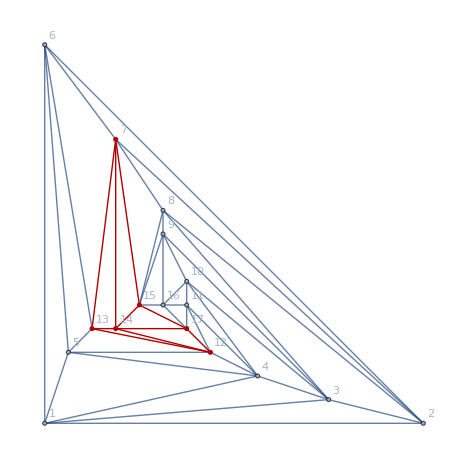

```mathematica
HighlightGraph[Graph[g,VertexLabels->"Name",GraphLayout->"PlanarEmbedding"],NeighborhoodGraph[g,14]]
```

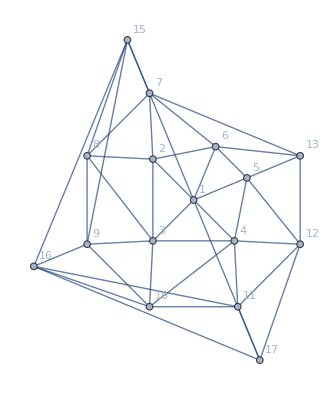

```mathematica
g2=Graph[VertexDelete[g,14],VertexLabels->"Name",GraphLayout->"RadialDrawing"]
```

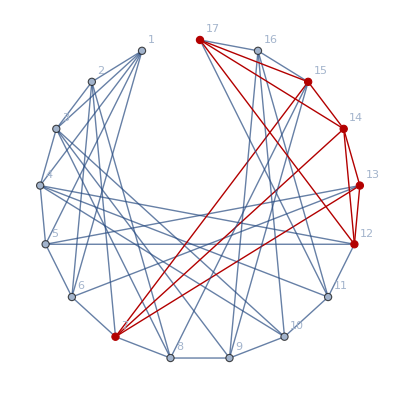

```mathematica
Graph[g,VertexLabels->"Name",GraphLayout->"CircularEmbedding",GraphHighlight->Join[EdgeList[NeighborhoodGraph[g,14]],VertexList[NeighborhoodGraph[g,14]]]]
```

```mathematica
14
```

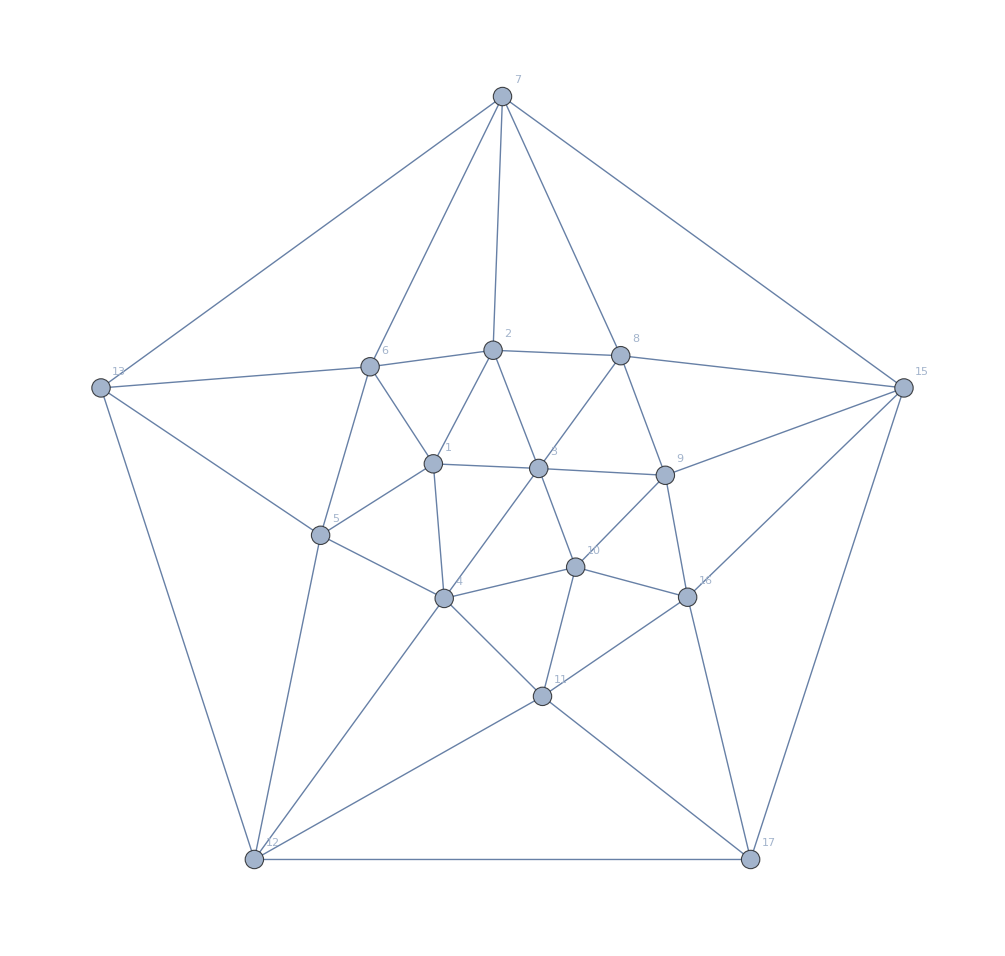

```mathematica
Graph[g2,VertexLabels->"Name",GraphLayout->"TutteEmbedding"]
```

```mathematica
ChromaticPolynomial[g2,4]/24
```

63

```mathematica
sols2=ToVarsLogical[g2,True]
```

{{x1→1,x2→2,x3→3,x4→2,x5→3,x6→4,x7→1,x8→4,x9→1,x10→4,x11→3,x12→1,x13→2,x15→3,x16→2,x17→4},{x1→1,x2→2,x3→3,x4→2,x5→3,x6→4,x7→1,x8→4,x9→1,x10→4,x11→3,x12→4,x13→2,x15→3,x16→2,x17→1},{x1→1,x2→2,x3→3,x4→2,x5→3,x6→4,x7→1,x8→4,x9→2,x10→1,x11→3,x12→1,x13→2,x15→3,x16→4,x17→2},{x1→1,x2→2,x3→3,x4→2,x5→3,x6→4,x7→1,x8→4,x9→2,x10→1,x11→3,x12→4,x13→2,x15→3,x16→4,x17→1},1505,{x1→4,x2→3,x3→2,x4→3,x5→2,x6→1,x7→4,x8→1,x9→3,x10→4,x11→2,x12→4,x13→3,x15→2,x16→1,x17→3},{x1→4,x2→3,x3→2,x4→3,x5→2,x6→1,x7→4,x8→1,x9→4,x10→1,x11→2,x12→1,x13→3,x15→2,x16→3,x17→4},{x1→4,x2→3,x3→2,x4→3,x5→2,x6→1,x7→4,x8→1,x9→4,x10→1,x11→2,x12→4,x13→3,x15→2,x16→3,x17→1}}
 |  |  |  |

```mathematica
TableForm[Map[First,Map[SolutionToPartition[#,{7,14,16,12,13},4]&,sols2]//Sort//Tally]]
```

7|EC|GD
7C|E|GD
7C|ED|G
7G|D|EC
7|C|E|GD
7|C|ED|G
7|D|EC|G
7C|D|E|G
7G|C|D|E

```mathematica
TableForm[Map[First,Map[SolutionToPartition[#]&,sols2]//Sort//Tally]]
```